# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

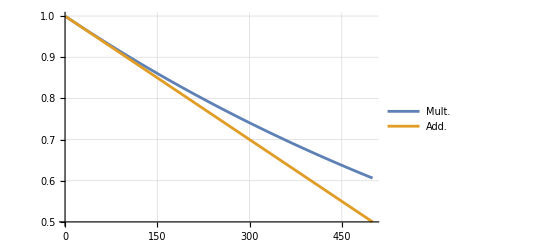

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params1={NN->1000,s->10^-4,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/10000,κ→1,L→2500,u→1/100000}

```mathematica
params2={NN->1000,s->10^-2,κ->1,L->10000,u->10^-5}
```

{NN→1000,s→1/100,κ→1,L→10000,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(10 (1-ⅇ^(-20 B))^3)/((1+ⅇ^(-20 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
bfun02[.2]
```

-0.840523

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-100]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

May need to adjust starting value (2nd argument) if this fails:

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.1]
```

0.075327

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.537592

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/1000,κ→1,L→10000,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-2.58592 (1-0.984304^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{999.363,75.4678,75.3271,75.327,75.327}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Doing it on HRI

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.40243 (1-0.995853^(1+τ))^2),999.976,245.999}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

```mathematica
{{x->0.,y->999.9758849338513},{x->500.,y->341.47926284834415},{x->1000.,y->256.92444267278876},{x->1500.,y->247.3500977052783},{x->2000.,y->246.16752998190728},{x->2500.,y->246.01970478874085},{x->3000.,y->246.0011980558869},{x->3500.,y->245.99888069501498},{x->4000.,y->245.99859051471174},{x->4500.,y->245.99855417817884},{x->5000.,y->245.99854962809712}}
```

{{x→0.,y→999.976},{x→500.,y→341.479},{x→1000.,y→256.924},{x→1500.,y→247.35},{x→2000.,y→246.168},{x→2500.,y→246.02},{x→3000.,y→246.001},{x→3500.,y→245.999},{x→4000.,y→245.999},{x→4500.,y→245.999},{x→5000.,y→245.999}}

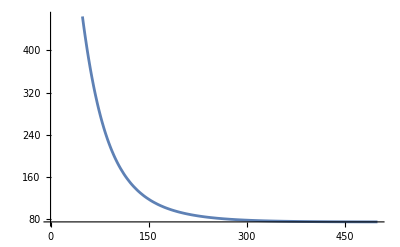

```mathematica
Plot[rAndL⟦1⟧,{τ,0,500}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.40243 (1-0.995853^(1+τ))^2),999.976,245.999}

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→31.3784},{τ→-22.3064}}

```mathematica
inv
```

{{τ→-63.2083 Log[1.56761×10^-16 (6.48085×10^15-1. √(4.20014×10^31-1.62424×10^31 Log[0.0132754471822349 y]))]},{τ→-63.2083 Log[1.5676141466587×10^-16 (6.4808455967368×10^15+√(4.2001359648743×10^31-1.6242351084045×10^31 Log[0.0132754471822349 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-63.2083 Log[1.56761×10^-16 (6.48085×10^15-1. √(4.20014×10^31-1.62424×10^31 Log[0.0132754471822349 y]))]

```mathematica
inv2/.y->660//N
```

31.3784

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}

```mathematica
xy1={xs,ys}//N
```

{{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332},{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,8.25471,16.4132,23.3044,30.1572,37.5272,45.9703,56.3333,70.313,92.5123,146.332},{999.363,906.959,814.556,722.152,629.749,537.345,444.941,352.538,260.134,167.731,75.327}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-81.8221 0.984304^(1+τ) (1-0.984304^(1+τ)) ⅇ^(-2.58592 (1-0.984304^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

13.5883

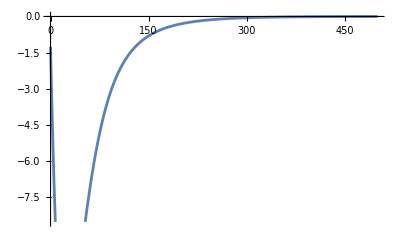

```mathematica
Plot[Nprime01p/.τ->t,{t,0,500}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Piecewise[{{999.363, x<14.6332}, {786.848, x<29.2663}, {594.823, x<43.8995}, {441.552, x<58.5327}, {332.31, x<73.1658}, {257.358, x<87.799}, {206.178, x<102.432}, {170.87, x<117.065}, {146.113, x<131.699}, {128.443, x<146.332}, {75.327, x>146.332}, {0., True}}]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{999.363, x<8.25471}, {906.959, x<16.4132}, {814.556, x<23.3044}, {722.152, x<30.1572}, {629.749, x<37.5272}, {537.345, x<45.9703}, {444.941, x<56.3333}, {352.538, x<70.313}, {260.134, x<92.5123}, {167.731, x<146.332}, {75.327, x>146.332}, {0., True}}]

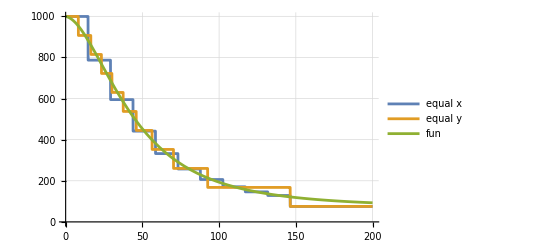

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,200},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

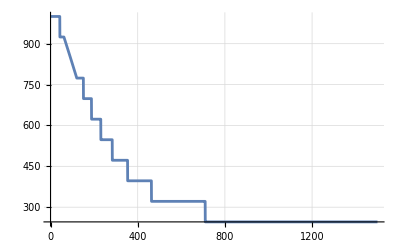

```mathematica
Plot[pwNe2/.x->t,{t,0,1500},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{999.363, x<8.25471}, {906.959, x<16.4132}, {814.556, x<23.3044}, {722.152, x<30.1572}, {629.749, x<37.5272}, {537.345, x<45.9703}, {444.941, x<56.3333}, {352.538, x<70.313}, {260.134, x<92.5123}, {167.731, x<146.332}, {75.327, x>146.332}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

75.327

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{1.2687,0.0000189017}

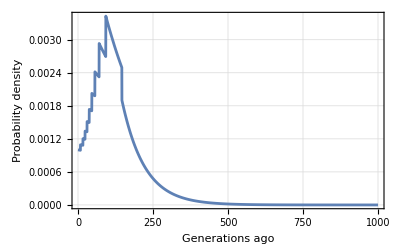

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{10.9735,167.245}

```mathematica
a01[[2]]
```

167.245

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{160.053,0.590828},{131.597,0.165204},{130.662,0.0797977},{129.91,0.049195},{129.089,0.0345729},{128.483,0.0263243},{128.033,0.0211587},{127.737,0.0176872},{127.534,0.0152318}}

```mathematica
Export["v05sfs10.txt", n10All]
```

v05sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{309.035,0.531369},{275.37,0.163102},{275.124,0.0796119},{274.903,0.0482794},{274.762,0.0331288},{274.419,0.0245788},{274.164,0.0192305},{273.985,0.0156329},{273.763,0.0130801},{273.665,0.0111938},{273.62,0.009755},{273.568,0.00862952},{273.41,0.00773077},{273.378,0.00700066},{273.254,0.00639882},{273.071,0.0058964},{273.047,0.00547223},{272.934,0.00511046},{272.761,0.00479899}}

```mathematica
Export["v05sfs20.txt", n20All]
```

v05sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{637.152,0.477226},{571.114,0.163187},{571.056,0.0830246},{570.799,0.0508778},{570.619,0.0347927},{570.717,0.0255721},{570.788,0.0197722},{570.718,0.0158693},{570.735,0.013105},{570.562,0.0110672},{570.584,0.00951624},{570.565,0.00830444},{570.589,0.00733689},{570.72,0.00655014},{570.344,0.00590039},{570.548,0.0053566},{570.556,0.00489619},{570.312,0.00450242},{570.314,0.00416265},{570.425,0.00386715},{570.262,0.00360836},{569.88,0.00338028},{569.651,0.00317814},{569.509,0.00299807},{569.467,0.0028369},{569.377,0.00269204},{569.82,0.00256131},{569.933,0.00244292},{570.01,0.00233533},{569.84,0.00223724},{569.817,0.00214754},{569.96,0.00206528},{569.866,0.00198964},{569.596,0.0019199},{569.55,0.00185543},{569.646,0.0017957},{569.633,0.00174022},{569.575,0.00168856},{569.683,0.00164037}}

```mathematica
Export["v05sfs40.txt", n40All]
```

v05sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1355.,0.423376},{1232.73,0.16072},{1228.76,0.0866361},{1227.7,0.0547893},{1226.77,0.0380736},{1226.42,0.0281753},{1226.,0.0218131},{1226.07,0.0174714},{1226.45,0.0143695},{1226.26,0.0120715},{1226.15,0.0103181},{1225.45,0.00894723},{1225.56,0.00785317},{1225.65,0.00696462},{1225.65,0.006232},{1232.41,0.00561997},{1226.1,0.00510273},{1226.2,0.00466114},{1226.22,0.00428069},{1226.27,0.00395024},{1225.83,0.00366111},{1225.65,0.00340647},{1226.03,0.00318084},{1225.66,0.00297983},{1225.77,0.00279985},{1225.7,0.00263795},{1225.78,0.00249172},{1225.85,0.00235911},{1225.84,0.00223842},{1225.66,0.00212822},{1225.69,0.00202727},{1225.99,0.00193454},{1225.91,0.00184912},{1225.81,0.00177024},{1226.18,0.00169722},{1225.84,0.00162949},{1225.97,0.00156652},{1225.71,0.00150786},{1225.67,0.00145313},{1225.77,0.00140196},{1225.7,0.00135404},{1225.76,0.00130911},{1225.97,0.00126691},{1225.75,0.00122721},{1225.74,0.00118982},{1225.9,0.00115457},{1226.6,0.00112128},{1225.67,0.00108981},{1225.59,0.00106004},{1225.73,0.00103183},{1225.75,0.00100507},{1225.3,0.00097968},{1354.98,0.000955551},{1490.47,0.000932604},{1494.31,0.000910761},{1486.33,0.000889952},{1489.96,0.00087011},{1491.8,0.000851177},{1496.15,0.000833095},{1482.35,0.000815814},{1491.39,0.000799285},{1260.54,0.000783465},{1224.94,0.000768312},{1224.35,0.000753789},{1225.05,0.000739858},{1225.1,0.000726488},{1225.03,0.000713647},{1225.16,0.000701307},{1225.18,0.00068944},{1225.34,0.00067802},{1224.93,0.000667025},{1225.53,0.000656432},{1225.27,0.00064622},{1225.01,0.000636369},{1225.01,0.000626861},{1224.75,0.000617679},{1224.65,0.000608807},{1224.41,0.000600229},{1224.51,0.00059193}}

```mathematica
Export["v05sfs80.txt", n80All]
```

v05sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11

#### Comeron 2002 params

Their α is our γ,
their β is Ne×μ with μ=(w+v), i.e. per-nuc. rates to del and back, respectively
Their w is our u, their v is our κu
Their γ is related to our κ:
γ_Com=v/(w+v)=κu/(u+κu)
Thus, κ=γ/(1-γ)
Their defaults are γ=0.45 and β_N=0.01, i.e.

```mathematica
.45/(1-.45)
```

0.818182